```mathematica
$Assumptions=wk∈Reals && wk > 0 && kappa∈Reals && kappa >3/2 && vpar∈Reals && vperp∈Reals && vperp >= 0 &&  kperp∈Reals && kperp>0&& kpar ∈Reals && kpar >= 0 &&n∈Integers  && Oc∈Reals && Oc > 0 && omega∈Reals && nu∈Reals && nu > 0  && n>=0 && vth∈Reals && vth > 0 ;
```

```mathematica
(* This is base of kappa distribution *)
f3DBase = (1+(vpar^2+vperp^2)/(kappa-3/2)/vth^2)^(-kappa-1)
```

(1+(vpar^2+vperp^2)/((-3/2+kappa) vth^2))^(-1-kappa)

```mathematica
(* Get the normalization factor by doing 1 over the zeroth moment of the base *)
f3DNorm = 1/Integrate[vperp*f3DBase,{vperp,0,Infinity},{vpar,-Infinity,Infinity},{phi,0,2*Pi}]
```

(4 √2 Gamma[1+kappa])/((-3+2 kappa)^(5/2) π^(3/2) vth^3 Gamma[-3/2+kappa])

```mathematica
(* Get total distribution by using base and normalization factor *)
f3D = f3DBase*f3DNorm
```

(4 √2 (1+(vpar^2+vperp^2)/((-3/2+kappa) vth^2))^(-1-kappa) Gamma[1+kappa])/((-3+2 kappa)^(5/2) π^(3/2) vth^3 Gamma[-3/2+kappa])

```mathematica
(* Show that distribution is normalized *)
Integrate[f3D*vperp,{vperp,0,Infinity},{vpar,-Infinity,Infinity},{phi,0,2*Pi}]
```

1

```mathematica
(* Show that the temperature of the kappa distribution is the same as the temperature of the Maxwellian distribution *)
Integrate[f3D*vperp*(vperp^2+vpar^2),{vperp,0,Infinity},{vpar,-Infinity,Infinity},{phi,0,2*Pi}]
Integrate[Exp[-(vpar^2+vperp^2)/vth^2]/Pi^(3/2)/vth^3*vperp*(vperp^2+vpar^2),{vpar,-Infinity,Infinity},{vperp,0,Infinity},{phi,0,2*Pi}]
```

(3 vth^2)/2

(3 vth^2)/2

```mathematica
(* Show in parts and then as a whole, that as we take the limit as kappa approaches infinity, we get a Maxwellian distribution *)
Limit[f3DBase,kappa->Infinity]
Limit[f3DNorm,kappa->Infinity]
Limit[f3D,kappa->Infinity]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

ⅇ^(-(vpar^2+vperp^2)/vth^2)

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

1/(π^(3/2) vth^3)

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

(ⅇ^(-(vpar^2+vperp^2)/vth^2))/(π^(3/2) vth^3)

(ⅇ^(-vpar^2))/(π^(3/2) vth^3)

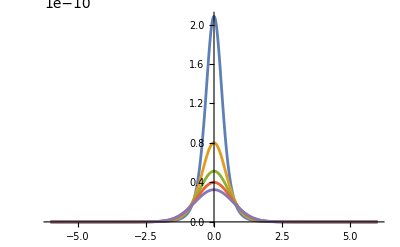

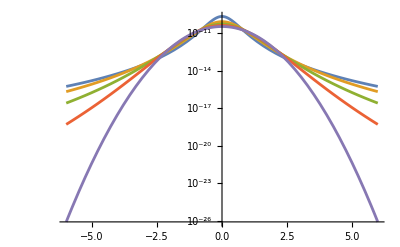

```mathematica
(* Plot kappa distributions *)
f3DNormV  = f3DNorm*(1+vpar^2/(kappa-3/2))^(-kappa-1)/.vth->1765.7642772705967;
fMaxwell = Exp[-vpar^2]/vth^3/Pi^(3/2);
Plot[{f3DNormV/.{kappa->2},f3DNormV/.{kappa->3},f3DNormV/.{kappa->5},f3DNormV/.{kappa->10},f3DNormV/.{kappa->10000},fMaxwell},{vpar,-6,6},PlotRange->All]
LogPlot[{f3DNormV/.{kappa->2},f3DNormV/.{kappa->3},f3DNormV/.{kappa->5},f3DNormV/.{kappa->10},f3DNormV/.{kappa->10000},fMaxwell},{vpar,-6,6},PlotRange->All]
```

```mathematica
]
```

```mathematica
(* This cell shows that there is no analytical solution to the integrals needed to get the IS scatter spectra *)Integrate[BesselJ[n,kperp*vperp/Oc]^2*f3D/(omega-kpar*vpar-n*Oc-I*nu)*vperp,{vpar,-Infinity,Infinity},{vperp,0,Infinity}]
```

∫_(-∞)^∞ ((√2 (1+vpar^2/((-3/2+kappa) vth^2))^-kappa ((kperp/Oc)^(2 kappa) (vpar^2+1/2 (-3+2 kappa) vth^2)^kappa Gamma[1/2+kappa] Gamma[1+n] Gamma[-kappa+n] HypergeometricPFQ[{1/2+kappa},{1+kappa-n,1+kappa+n},(kperp^2 (vpar^2+1/2 (-3+2 kappa) vth^2))/Oc^2]+2^(-2 n) (kperp/Oc)^(2 n) √π (vpar^2-(3 vth^2)/2+kappa vth^2)^n Gamma[kappa-n] Gamma[1+kappa+n] HypergeometricPFQ[{1/2+n},{1-kappa+n,1+2 n},(kperp^2 (vpar^2+1/2 (-3+2 kappa) vth^2))/Oc^2]))/((-3+2 kappa)^(3/2) π^2 (-ⅈ nu-n Oc+omega-kpar vpar) vth Gamma[-3/2+kappa] Gamma[1+n] Gamma[1+kappa+n]))ⅆvpar